```mathematica
SetOptions[$FrontEndSession,"ExportTypesetOptions"->{"PageWidth"->1000}]
```

## Point Plot Generator

```mathematica
Clear[f,g]
```

```mathematica
f[x_]:=Piecewise[{{Cos[x],x≤Pi/2},{0,x>Pi/2}}]
```

```mathematica
f[x_]:=InterpolatingPolynomial[{-1,0,2,2},x]*2
```

```mathematica
polarpts=Flatten[{Table[{0+i,Pi/6+i,Pi/4+i,Pi/3+i},{i,{0,Pi/2,Pi,3Pi/2}}],2Pi}]
```

{0,π/6,π/4,π/3,π/2,(2 π)/3,(3 π)/4,(5 π)/6,π,(7 π)/6,(5 π)/4,(4 π)/3,(3 π)/2,(5 π)/3,(7 π)/4,(11 π)/6,2 π}

```mathematica
list=Table[{2Cos[x](N[Cos[2x]]),2Sin[x](N[Cos[2x]])},{x,polarpts}];
```

```mathematica
list1=Table[6{Cos[t],Sin[t]},{t,0,Pi,Pi/30.}];
list2=Reverse[Table[5{Cos[t],Sin[t]},{t,0,Pi,Pi/30.}]];
list=Flatten[{list1,list2},1];
```

```mathematica
list=Table[{i,Log[i]/i^2},{i,1,20}]//N
```

{{1.,0.},{2.,0.173287},{3.,0.122068},{4.,0.0866434},{5.,0.0643775},{6.,0.0497711},{7.,0.0397125},{8.,0.0324913},{9.,0.0271262},{10.,0.0230259},{11.,0.0198173},{12.,0.0172563},{13.,0.0151772},{14.,0.0134646},{15.,0.0120358},{16.,0.0108304},{17.,0.00980351},{18.,0.0089209},{19.,0.00815634},{20.,0.00748933}}

```mathematica
list=Table[.25((approx[1x,7]+.5)/15+1){Cos[x],Sin[x]}+{-.5,.5},{x,0,2Pi,2Pi/100}];
```

```mathematica
list=Table[(.1)(.1Cos[3t]+.05Sin[5t]+1){Cos[t],Sin[t]}+{-.2,-1.75},{t,0,2Pi,Pi/25}];
```

```mathematica
mynumstyle[x_]:=If[Abs[x]<0.0001,0,NumberForm[x,4]]
liststring="";
For[i=1,i≤Length[list],i++,
liststring=StringJoin[liststring,"(",ToString[mynumstyle[list[[i,1]]]],",",ToString[mynumstyle[list[[i,2]]]],")"];];
CopyToClipboard[liststring];
liststring
```

(1.8,0)(1.805,0.08795)(1.777,0.1713)(1.718,0.2386)(1.642,0.2848)(1.566,0.3161)(1.501,0.3458)(1.447,0.3858)(1.392,0.4371)(1.327,0.4889)(1.25,0.525)(1.165,0.5337)(1.083,0.514)(1.009,0.4738)(0.9429,0.4228)(0.8839,0.3661)(0.833,0.303)(0.7957,0.2315)(0.7786,0.1532)(0.7827,0.07401)(0.8,0)(0.8176,-0.06848)(0.8262,-0.1377)(0.8272,-0.2154)(0.833,-0.303)(0.8589,-0.3911)(0.9135,-0.4632)(0.9926,-0.5053)(1.083,-0.514)(1.171,-0.4988)(1.25,-0.475)(1.322,-0.454)(1.392,-0.4371)(1.463,-0.4173)(1.531,-0.3863)(1.591,-0.3411)(1.642,-0.2848)(1.687,-0.2225)(1.73,-0.1559)(1.77,-0.08242)(1.8,0)

```mathematica
mynumstyle[x_]:=If[Abs[x]<0.0001,0,NumberForm[x,4]]
liststring="";
For[i=1,i≤Length[list],i++,
liststring=StringJoin[liststring,"(",ToString[mynumstyle[list[[i,1]]]],",",ToString[mynumstyle[list[[i,2]]]],") -- "];];
liststring
```

(-1.021,-0.738) -- (-1.021,-0.738) --

```mathematica
liststring="";
For[i=1,i≤Length[list],i++,
liststring=StringJoin[liststring,ToString[mynumstyle[list[[i,1]]]],"/",ToString[mynumstyle[list[[i,2]]]],","];];
```

```mathematica
liststring
```

0.6928/0.4,0.6857/0.412,0.6784/0.4239,0.6709/0.4357,0.6632/0.4474,0.6553/0.4589,0.6472/0.4702,0.6389/0.4815,0.6304/0.4925,0.6217/0.5035,0.6128/0.5142,0.6038/0.5248,0.5945/0.5353,0.5851/0.5456,0.5755/0.5557,0.5657/0.5657,

```mathematica
Plot[f[x],{x,0,3}]
```

### For Contour Plots

```mathematica
f[x_,y_]:=Cos[y]Sin[x]
```

```mathematica
f[x_,y_]:=(x+y)/(x^2+y^2+1)
```

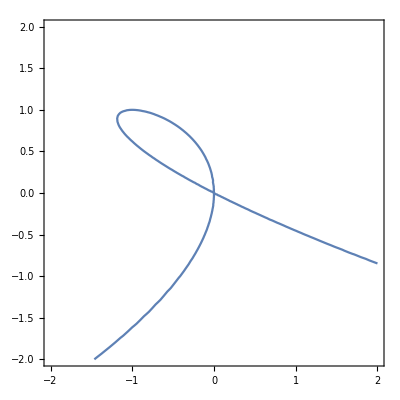

```mathematica
contour=ContourPlot[f[x,y]==0,{x,-2,2},{y,-2,2},ContourShading->None,Contours->{0}]
listall=Cases[Normal@contour,Line[x_]:>x,Infinity];
```

```mathematica
Length[listall]
```

2

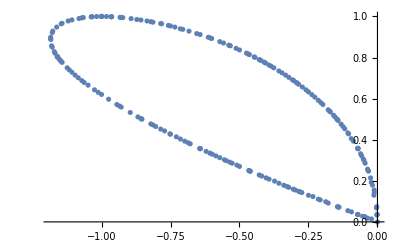

```mathematica
ListPlot[listall[[2]]]
```

```mathematica
points=Take[listall[[1]],{1,-1,1}];
```

```mathematica
list=listall[[1]];
```

```mathematica
list=Map[{#[[1]],#[[2]],f[#[[1]],#[[2]]]}&,points];
```

```mathematica
Map[f[#[[1]],#[[2]]]&,listall[[All,1]]]
```

{0.433237}

```mathematica
mynumstyle[x_]:=If[Abs[x]<0.0001,0,NumberForm[x,4]]
liststring="";
For[i=1,i≤Length[list],i++,
liststring=StringJoin[liststring,"(",ToString[mynumstyle[list[[i,1]]]],",",ToString[mynumstyle[list[[i,2]]]],")"];];
liststring
```

(2.,-0.8472)(1.984,-0.8412)(1.903,-0.8113)(1.857,-0.7917)(1.799,-0.772)(1.754,-0.7536)(1.714,-0.738)(1.696,-0.7324)(1.647,-0.7143)(1.593,-0.6926)(1.571,-0.6824)(1.52,-0.6632)(1.491,-0.6523)(1.466,-0.6429)(1.429,-0.6273)(1.388,-0.612)(1.288,-0.5714)(1.286,-0.5709)(1.286,-0.5706)(1.284,-0.5699)(1.214,-0.5411)(1.185,-0.5297)(1.164,-0.5208)(1.143,-0.5122)(1.134,-0.509)(1.111,-0.5)(1.083,-0.4882)(1.071,-0.4826)(1.042,-0.4708)(1.033,-0.4671)(1.,-0.4528)(0.9823,-0.4462)(0.9643,-0.4383)(0.9405,-0.4286)(0.9321,-0.425)(0.9286,-0.4233)(0.9192,-0.4192)(0.8819,-0.4039)(0.8571,-0.3924)(0.7942,-0.3656)(0.7857,-0.3623)(0.7818,-0.3611)(0.7723,-0.3571)(0.7143,-0.331)(0.6812,-0.3188)(0.6429,-0.2999)(0.6324,-0.2961)(0.6096,-0.2857)(0.6071,-0.2846)(0.605,-0.2836)(0.5831,-0.274)(0.5714,-0.2685)(0.5404,-0.2547)(0.5357,-0.2527)(0.5337,-0.252)(0.5292,-0.25)(0.5,-0.2366)(0.4841,-0.2302)(0.4483,-0.2143)(0.4351,-0.2078)(0.4286,-0.204)(0.4092,-0.195)(0.386,-0.1854)(0.3716,-0.1786)(0.3571,-0.1714)(0.3369,-0.1631)(0.3214,-0.1547)(0.2948,-0.1429)(0.2887,-0.1398)(0.2857,-0.1381)(0.2767,-0.1338)(0.2644,-0.1284)(0.25,-0.1212)(0.24,-0.1171)(0.2192,-0.1071)(0.2143,-0.1044)(0.1906,-0.09509)(0.1786,-0.0872)(0.1674,-0.08262)(0.1449,-0.07143)(0.1436,-0.07069)(0.1429,-0.07019)(0.1402,-0.06876)(0.1191,-0.05949)(0.1071,-0.05265)(0.09493,-0.04793)(0.07185,-0.03571)(0.07143,-0.0354)(0.07061,-0.0349)(0.0461,-0.02533)(0.03571,-0.01754)(0.02148,-0.01423)(0,0)(0,0)(-0.0008163,-0.0349)(-0.0005102,-0.03571)(-0.000383,-0.0361)(-0.002664,-0.06876)(-0.002268,-0.07143)(-0.002059,-0.07349)(-0.005456,-0.1017)(-0.00492,-0.1071)(-0.00541,-0.1126)(-0.009061,-0.1338)(-0.00907,-0.1429)(-0.009254,-0.1521)(-0.01449,-0.1786)(-0.01837,-0.1959)(-0.01848,-0.1971)(-0.02119,-0.2143)(-0.0244,-0.2256)(-0.02726,-0.2415)(-0.02938,-0.25)(-0.03084,-0.2549)(-0.03571,-0.2743)(-0.03813,-0.2857)(-0.04587,-0.3113)(-0.05211,-0.3378)(-0.05856,-0.3571)(-0.06241,-0.3662)(-0.07077,-0.3929)(-0.07143,-0.3945)(-0.08076,-0.4192)(-0.08339,-0.4286)(-0.09044,-0.4476)(-0.1006,-0.4708)(-0.1071,-0.4868)(-0.1122,-0.5)(-0.1221,-0.5208)(-0.1279,-0.5357)(-0.1429,-0.5668)(-0.1443,-0.57)(-0.1448,-0.5714)(-0.1467,-0.5753)(-0.156,-0.594)(-0.1623,-0.6071)(-0.1681,-0.6177)(-0.1717,-0.625)(-0.1786,-0.6379)(-0.1803,-0.6412)(-0.1811,-0.6429)(-0.184,-0.6482)(-0.1928,-0.6643)(-0.2004,-0.6786)(-0.2143,-0.7022)(-0.2186,-0.71)(-0.2208,-0.7143)(-0.2301,-0.7301)(-0.2453,-0.7547)(-0.2637,-0.7857)(-0.2729,-0.7986)(-0.2857,-0.817)(-0.3011,-0.8418)(-0.3105,-0.8571)(-0.3299,-0.8843)(-0.3571,-0.9227)(-0.3595,-0.9262)(-0.3609,-0.9286)(-0.371,-0.9424)(-0.4139,-1.)(-0.4209,-1.008)(-0.4286,-1.016)(-0.4845,-1.087)(-0.5288,-1.143)(-0.55,-1.164)(-0.5714,-1.185)(-0.6173,-1.24)(-0.6568,-1.286)(-0.6862,-1.314)(-0.7143,-1.34)(-0.7566,-1.386)(-0.7966,-1.429)(-0.8285,-1.457)(-0.8571,-1.482)(-0.9017,-1.527)(-0.9475,-1.571)(-0.9761,-1.595)(-1.,-1.614)(-1.052,-1.663)(-1.109,-1.714)(-1.128,-1.729)(-1.143,-1.74)(-1.206,-1.794)(-1.282,-1.857)(-1.284,-1.859)(-1.286,-1.86)(-1.3,-1.871)(-1.364,-1.922)(-1.372,-1.929)(-1.429,-1.972)(-1.444,-1.984)(-1.464,-2.)

```mathematica
mynumstyle[x_]:=If[Abs[x]<0.0001,0,NumberForm[x,4]]
liststring="";
For[i=1,i≤Length[list],i++,
liststring=StringJoin[liststring,"(",ToString[mynumstyle[list[[i,1]]]],",",ToString[mynumstyle[list[[i,2]]]],",",ToString[mynumstyle[list[[i,3]]]],")"];];
liststring
```

```mathematica
ListPointPlot3D[Map[{#[[1]],#[[2]],f[#[[1]],#[[2]]]}&,list[[3]]]]
```

### Closed Curves (BSpline...)

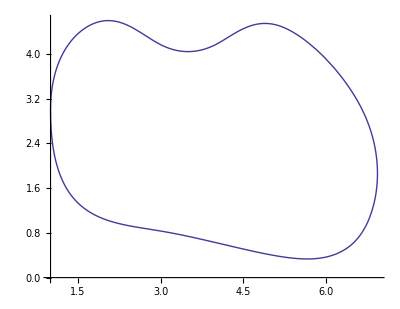

```mathematica
pts={{0,1},{0,2},{1,3},{2,2},{3,2},{4,3},{6,1},{6,-1},{5,-2},{2,-1},{0,-1},{0,1}};
f=BSplineFunction[pts];
ParametricPlot[f[t]+{1,2},{t,0,1}]
```

```mathematica
list=Table[f[x]+{1,2},{x,0,1,1./50}];
```

```mathematica
liststring="";
For[i=1,i≤Length[list],i++,
liststring=StringJoin[liststring,"(",ToString[mynumstyle[list[[i,1]]]],",",ToString[mynumstyle[list[[i,2]]]],")"];];
liststring
```

(1.,3.)(1.045,3.492)(1.167,3.889)(1.346,4.196)(1.56,4.414)(1.79,4.546)(2.015,4.596)(2.226,4.574)(2.425,4.501)(2.615,4.397)(2.799,4.282)(2.98,4.177)(3.16,4.099)(3.34,4.054)(3.52,4.042)(3.7,4.062)(3.88,4.114)(4.06,4.198)(4.242,4.306)(4.432,4.415)(4.636,4.503)(4.859,4.544)(5.107,4.518)(5.385,4.402)(5.681,4.203)(5.979,3.938)(6.261,3.624)(6.508,3.279)(6.705,2.92)(6.84,2.562)(6.917,2.211)(6.943,1.873)(6.922,1.553)(6.861,1.258)(6.766,0.9942)(6.634,0.7662)(6.46,0.5803)(6.238,0.4424)(5.962,0.3583)(5.626,0.3337)(5.229,0.3693)(4.781,0.4503)(4.292,0.5591)(3.774,0.6783)(3.24,0.7904)(2.701,0.8805)(2.182,0.9817)(1.717,1.168)(1.342,1.517)(1.091,2.102)(1.,3.)

### For 3 D printing ....

```mathematica
list=Table[{1.35,t,-.5(1.35-1)^2-.5t^2+2},{t,-.74,.74,(.74*2)/10}];
```

```mathematica
35
```

```mathematica
list=Table[{Pi Cos[x*Pi/180],Pi Sin[x*Pi/180],0},{x,180,325,15.}];
```

```mathematica
list=Join[list1,list2];
```

```mathematica
liststring="";
For[i=1,i≤Length[list],i++,
liststring=StringJoin[liststring,"(axis cs:",ToString[mynumstyle[list[[i,1]]]],",",ToString[mynumstyle[list[[i,2]]]],",",ToString[mynumstyle[list[[i,3]]]],")--"];];
liststring
```

(axis cs:1.35,-0.74,1.665)--(axis cs:1.35,-0.592,1.764)--(axis cs:1.35,-0.444,1.84)--(axis cs:1.35,-0.296,1.895)--(axis cs:1.35,-0.148,1.928)--(axis cs:1.35,0,1.939)--(axis cs:1.35,0.148,1.928)--(axis cs:1.35,0.296,1.895)--(axis cs:1.35,0.444,1.84)--(axis cs:1.35,0.592,1.764)--(axis cs:1.35,0.74,1.665)--

```mathematica
Radians[90]
```

```mathematica
list
```

{{0.409576,-0.286788,0.8},{0.433013,-0.25,0.8},{0.453154,-0.211309,0.8},{0.469846,-0.17101,0.8},{0.482963,-0.12941,0.8},{0.492404,-0.0868241,0.8},{0.498097,-0.0435779,0.8},{0.5,0.,0.8},{0.498097,0.0435779,0.8},{0.492404,0.0868241,0.8},{0.482963,0.12941,0.8},{0.469846,0.17101,0.8},{0.453154,0.211309,0.8},{0.433013,0.25,0.8},{0.409576,0.286788,0.8},{0.383022,0.321394,0.8},{0.353553,0.353553,0.8},{0.321394,0.383022,0.8},{0.286788,0.409576,0.8},{0.25,0.433013,0.8},{0.211309,0.453154,0.8},{0.17101,0.469846,0.8},{0.12941,0.482963,0.8},{0.0868241,0.492404,0.8},{0.0435779,0.498097,0.8},{0.,0.5,0.8},{-0.0435779,0.498097,0.8},{-0.0868241,0.492404,0.8},{-0.12941,0.482963,0.8},{-0.17101,0.469846,0.8},{-0.211309,0.453154,0.8},{-0.25,0.433013,0.8},{-0.286788,0.409576,0.8},{-0.321394,0.383022,0.8},{-0.353553,0.353553,0.8},{-0.383022,0.321394,0.8},{-0.409576,0.286788,0.8},{-0.433013,0.25,0.8},{{-0.433013,0.25,0.64},{-0.409576,0.286788,0.64},{-0.383022,0.321394,0.64},{-0.353553,0.353553,0.64},{-0.321394,0.383022,0.64},{-0.286788,0.409576,0.64},{-0.25,0.433013,0.64},{-0.211309,0.453154,0.64},{-0.17101,0.469846,0.64},{-0.12941,0.482963,0.64},{-0.0868241,0.492404,0.64},{-0.0435779,0.498097,0.64},{0.,0.5,0.64},{0.0435779,0.498097,0.64},{0.0868241,0.492404,0.64},{0.12941,0.482963,0.64},{0.17101,0.469846,0.64},{0.211309,0.453154,0.64},{0.25,0.433013,0.64},{0.286788,0.409576,0.64},{0.321394,0.383022,0.64},{0.353553,0.353553,0.64},{0.383022,0.321394,0.64},{0.409576,0.286788,0.64},{0.433013,0.25,0.64},{0.453154,0.211309,0.64},{0.469846,0.17101,0.64},{0.482963,0.12941,0.64},{0.492404,0.0868241,0.64},{0.498097,0.0435779,0.64},{0.5,0.,0.64},{0.498097,-0.0435779,0.64},{0.492404,-0.0868241,0.64},{0.482963,-0.12941,0.64},{0.469846,-0.17101,0.64},{0.453154,-0.211309,0.64},{0.433013,-0.25,0.64},{0.409576,-0.286788,0.64}}}

```mathematica
ListPlot[list]
```

```mathematica
ParametricPlot[{{x,Sin[x]},{Sin[x],x},{x,x}},{x,-Pi/2,Pi/2}]
```

```mathematica
Pi/4//N
```

0.785398

```mathematica
Sqrt[3]/2//N
```

0.866025

#### Writing Lists to a File

```mathematica
SetDirectory["C:\\Documents and Settings\\hartmangn\\My Documents\\Text Projects\\Calculus\\text"]
```

C:\Documents and Settings\hartmangn\My Documents\Text Projects\Calculus\text

```mathematica
str=OpenWrite["datapoints.tex"]
(*liststring="";*)
For[i=1,i≤Length[list],i++,
WriteString[str,StringJoin["(",ToString[list[[i,1]]],",",ToString[list[[i,2]]],") "]];];
(*Write[str,liststring]*)
Close[str];
```

OutputStream[datapoints.tex,35]

```mathematica
f[x_]:=Piecewise[{{x^2-2x+3,x≤1},{x,x>1}}]
```

#### Making Tables in LaTeX

```mathematica
maketable[a_]:=TeXForm[TableForm[Table[{x,f[x]},{x,{a-.1,a-.01,a-.001,a+.001,a+.01,a+.1}}]]]
```

```mathematica
maketable[0]
```

\begin{array}{cc}
 -0.1 & 0.544021 \\
 -0.01 & 0.506366 \\
 -0.001 & -0.82688 \\
 0.001 & 0.82688 \\
 0.01 & -0.506366 \\
 0.1 & -0.544021
\end{array}

```mathematica
TeXForm[TableForm[Table[{h,(f[1+h]-f[1])/h},{h,{-.5,-.1,-.01,.01,.1,.5}}]]]
```

\begin{array}{cc}
 -0.5 & 9.25 \\
 -0.1 & 8.65 \\
 -0.01 & 8.515 \\
 0.01 & 8.485 \\
 0.1 & 8.35 \\
 0.5 & 7.75
\end{array}

#### Implicit Plots

```mathematica
clista=clist;
```

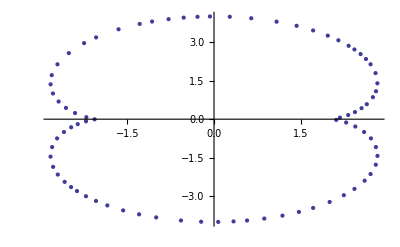

80

```mathematica
clistaa={};
For[i=1,i≤Length[clista]/10,i++,
clistaa=Append[clistaa,clista[[10i]]];
];
ListPlot[clistaa]
Length[clistaa]
```

```mathematica
list=clistaa;
```

```mathematica
Length[list]
```

80

```mathematica
clistaa=Transpose[clistaa];
clistaa[[1,All]]=NumberForm[#,3]&/@clistaa[[1,All]];
clistaa[[2,All]]=NumberForm[#,3]&/@clistaa[[2,All]];
clistaa=Transpose[clistaa];
```

```mathematica
list=clistaa;
liststring="";
For[i=1,i≤Length[list],i++,
liststring=StringJoin[liststring,"(",ToString[list[[i,1]]],",",ToString[list[[i,2]]],") "];];
liststring
```

(-1.91,-1.57) (-1.82,-1.61) (-1.68,-1.61) (-1.7,-1.49) (-1.74,-1.38) (-1.76,-1.28) (-1.64,-1.26) (-1.54,-1.29) (-1.36,-1.35) (-1.2,-1.42) (-1.09,-1.46) (-0.989,-1.49) (-0.86,-1.5) (-0.714,-1.45) (-0.566,-1.35) (-0.327,-1.18) (-0.15,-1.08) (          -16
-5.94 × 10,-1.) (0.107,-0.947) (0.216,-0.895) (0.332,-0.832) (0.429,-0.755) (0.464,-0.623) (0.429,-0.52) (0.308,-0.335) (0.142,-0.144) (-0.071,0.0714) (-0.239,0.261) (-0.336,0.45) (-0.336,0.622) (-0.278,0.757) (-0.17,0.884) (-0.046,0.975) (0.0714,1.03) (0.216,1.07) (0.48,1.09) (0.714,1.07) (0.929,1.05) (1.15,1.07) (1.24,1.13) (1.27,1.25) (1.28,1.37) (1.29,1.49) (1.36,1.58) (1.47,1.57) (1.59,1.52) (1.68,1.48) (1.79,1.43) (1.89,1.39) (1.98,1.36) (1.98,1.6)

```mathematica
ContourPlot[Re[x]^(.666666)+Re[y]^(.66666)==8,{x,-25,25},{y,-25,25}]
```

```mathematica
FullForm[ContourPlot[Sin[x^2y^2]+y^3==x+y,{x,-2,2},{y,-2,2},MaxRecursion->2]]
```

Graphics[GraphicsComplex[List[List[-2.,-1.53035],List[-1.99633,-1.53204],List[-1.9884,-1.53571],List[-1.9718,-1.54323],List[-1.96429,-1.54664],List[-1.94746,-1.5546],List[-1.94355,-1.55645],List[-1.92857,-1.56283],List[-1.92202,-1.56487],List[-1.90985,-1.57143],List[-1.89286,-1.579],List[-1.87851,-1.58578],List[-1.875,-1.58723],List[-1.87346,-1.58775],List[-1.85714,-1.59412],List[-1.84802,-1.59802],List[-1.82658,-1.60714],List[-1.82293,-1.60864],List[-1.82143,-1.60926],List[-1.81765,-1.61092],List[-1.79613,-1.61756],List[-1.78571,-1.62075],List[-1.76925,-1.6264],List[-1.76504,-1.62782],List[-1.75,-1.6306],List[-1.73818,-1.63104],List[-1.72422,-1.63293],List[-1.71429,-1.62963],List[-1.69667,-1.62476],List[-1.68448,-1.60714],List[-1.68221,-1.6035],List[-1.67952,-1.57238],List[-1.67946,-1.57143],List[-1.67944,-1.57056],List[-1.68422,-1.54136],List[-1.68528,-1.53571],List[-1.68718,-1.52711],List[-1.69123,-1.51266],List[-1.69511,-1.5],List[-1.69985,-1.48557],List[-1.70364,-1.47493],List[-1.70743,-1.46429],List[-1.70919,-1.45919],List[-1.71429,-1.44603],List[-1.71912,-1.43341],List[-1.72112,-1.42857],List[-1.72604,-1.41681],List[-1.72923,-1.4078],List[-1.73494,-1.39286],List[-1.73901,-1.38187],List[-1.74801,-1.35913],List[-1.74853,-1.35714],List[-1.7488,-1.35595],List[-1.75,-1.35115],List[-1.75614,-1.32757],List[-1.7579,-1.32143],List[-1.76029,-1.31113],List[-1.75876,-1.29448],List[-1.75814,-1.28571],List[-1.75692,-1.27879],List[-1.75,-1.27253],List[-1.73914,-1.26086],List[-1.72082,-1.25653],List[-1.71429,-1.25494],List[-1.71057,-1.25372],List[-1.683,-1.25443],List[-1.67857,-1.25451],List[-1.67418,-1.25439],List[-1.65104,-1.25818],List[-1.64286,-1.25949],List[-1.63191,-1.26095],List[-1.62084,-1.26369],List[-1.60714,-1.26652],List[-1.60193,-1.26786],List[-1.592,-1.27057],List[-1.58495,-1.27219],List[-1.57143,-1.27607],List[-1.56415,-1.27843],List[-1.53961,-1.28571],List[-1.53571,-1.28687],List[-1.51037,-1.29609],List[-1.5,-1.29893],List[-1.47987,-1.30585],List[-1.46429,-1.3116],List[-1.45723,-1.31437],List[-1.43827,-1.32143],List[-1.42857,-1.32504],List[-1.40564,-1.33421],List[-1.36322,-1.35106],List[-1.35714,-1.35345],List[-1.35455,-1.35455],List[-1.34847,-1.35714],List[-1.32143,-1.36824],List[-1.30389,-1.37532],List[-1.28571,-1.38319],List[-1.26296,-1.39286],List[-1.25376,-1.39661],List[-1.24053,-1.40232],List[-1.21429,-1.41302],List[-1.20332,-1.41761],List[-1.17975,-1.42739],List[-1.17857,-1.42784],List[-1.17671,-1.42857],List[-1.15231,-1.43802],List[-1.14286,-1.44164],List[-1.12658,-1.44801],List[-1.12144,-1.44999],List[-1.10714,-1.45494],List[-1.10023,-1.45737],List[-1.08929,-1.4614],List[-1.08065,-1.46429],List[-1.07367,-1.46653],List[-1.07143,-1.46734],List[-1.06689,-1.46882],List[-1.04626,-1.47483],List[-1.03571,-1.47782],List[-1.01842,-1.4827],List[-1.01687,-1.48313],List[-1.,-1.48677],List[-0.989099,-1.4891],List[-0.971666,-1.49262],List[-0.964286,-1.49363],List[-0.958669,-1.49438],List[-0.930842,-1.49773],List[-0.928571,-1.49784],List[-0.926503,-1.49793],List[-0.89395,-1.49891],List[-0.892857,-1.49886],List[-0.891652,-1.4988],List[-0.860403,-1.49674],List[-0.857143,-1.49626],List[-0.852391,-1.49525],List[-0.821429,-1.48985],List[-0.801184,-1.48453],List[-0.785714,-1.47967],List[-0.752768,-1.46705],List[-0.75,-1.46605],List[-0.748768,-1.46552],List[-0.746106,-1.46429],List[-0.714286,-1.44838],List[-0.701503,-1.44135],List[-0.678931,-1.42857],List[-0.678571,-1.42835],List[-0.656986,-1.41444],List[-0.642857,-1.40532],List[-0.623987,-1.39286],List[-0.614159,-1.38584],List[-0.573349,-1.35714],List[-0.571429,-1.35565],List[-0.566124,-1.35184],List[-0.531002,-1.32614],List[-0.5,-1.30273],List[-0.474576,-1.28571],List[-0.448221,-1.26606],List[-0.428571,-1.25121],List[-0.40619,-1.23667],List[-0.372209,-1.21429],List[-0.363533,-1.2079],List[-0.357143,-1.20313],List[-0.327016,-1.18416],List[-0.320224,-1.17978],List[-0.318191,-1.17857],List[-0.285714,-1.15767],List[-0.276511,-1.15206],List[-0.260101,-1.14286],List[-0.232031,-1.12511],List[-0.214286,-1.11478],List[-0.200385,-1.10714],List[-0.186769,-1.09895],List[-0.149771,-1.07834],List[-0.142857,-1.07437],List[-0.140828,-1.07346],List[-0.136633,-1.07143],List[-0.0945669,-1.04829],List[-0.0714286,-1.0364],List[-0.0699927,-1.03571],List[-0.0476093,-1.02382],List[-0.0357143,-1.01757],List[-8.72865×10^-16,-1.],List[-5.93918×10^-16,-1.],List[-4.44089×10^-16,-1.],List[1.65974×10^-17,-1.],List[0.0238082,-0.988094],List[0.0357143,-0.981794],List[0.047745,-0.976316],List[0.0704171,-0.965297],List[0.0714286,-0.964797],List[0.0725834,-0.964286],List[0.0956686,-0.952811],List[0.107143,-0.946984],List[0.119883,-0.941312],List[0.139691,-0.931737],List[0.142857,-0.930181],List[0.143987,-0.929701],List[0.146529,-0.928571],List[0.178571,-0.912378],List[0.192052,-0.906338],List[0.209427,-0.897716],List[0.214286,-0.895269],List[0.215991,-0.894563],List[0.219663,-0.892857],List[0.239748,-0.882605],List[0.25,-0.876763],List[0.263347,-0.87049],List[0.282652,-0.860205],List[0.285714,-0.858555],List[0.286697,-0.858125],List[0.288651,-0.857143],List[0.321429,-0.837803],List[0.332173,-0.832173],List[0.339286,-0.827674],List[0.349599,-0.821429],List[0.354117,-0.818403],List[0.357143,-0.816247],List[0.373513,-0.805058],List[0.375294,-0.803866],List[0.392857,-0.789962],List[0.398777,-0.785714],List[0.414296,-0.771439],List[0.428571,-0.755496],List[0.433934,-0.75],List[0.44572,-0.732852],List[0.446296,-0.73201],List[0.45574,-0.714286],List[0.464286,-0.684476],List[0.465671,-0.679956],List[0.465943,-0.678571],List[0.46589,-0.676967],List[0.46738,-0.642857],List[0.464286,-0.623469],List[0.462248,-0.609181],List[0.461945,-0.607143],List[0.461148,-0.604005],List[0.454415,-0.5813],List[0.451323,-0.571429],List[0.446429,-0.558887],List[0.444954,-0.555046],List[0.442976,-0.550119],List[0.43675,-0.535714],List[0.428571,-0.519912],List[0.421901,-0.506671],List[0.418923,-0.5],List[0.406264,-0.477693],List[0.396176,-0.460967],List[0.376,-0.428571],List[0.368027,-0.417688],List[0.357143,-0.403195],List[0.338475,-0.375811],List[0.325242,-0.357143],List[0.307746,-0.335111],List[0.285714,-0.308189],List[0.276014,-0.295415],List[0.268346,-0.285714],List[0.243417,-0.256583],List[0.214286,-0.223554],List[0.210072,-0.218499],List[0.206426,-0.214286],List[0.176086,-0.181057],List[0.142857,-0.145602],List[0.141556,-0.144158],List[0.140347,-0.142857],List[0.0714286,-0.0717791],List[0.0712573,-0.0715999],List[0.07109,-0.0714286],List[0.0356922,-0.0357363],List[7.21678×10^-13,-7.22566×10^-13],List[4.44089×10^-16,-4.44089×10^-16],List[2.94767×10^-19,2.94767×10^-19],List[-4.44089×10^-16,4.48643×10^-16],List[-0.0710383,0.0714286],List[-0.0712298,0.0716273],List[-0.0714286,0.071834],List[-0.13954,0.142857],List[-0.141125,0.144589],List[-0.142857,0.146577],List[-0.175013,0.182129],List[-0.20253,0.214286],List[-0.207797,0.220775],List[-0.214286,0.229443],List[-0.239082,0.260918],List[-0.256903,0.285714],List[-0.26837,0.303058],List[-0.285714,0.332842],List[-0.29502,0.347837],List[-0.300005,0.357143],List[-0.312507,0.383936],List[-0.318042,0.396244],List[-0.321429,0.405452],List[-0.329832,0.428571],List[-0.335727,0.449988],List[-0.339319,0.464286],List[-0.342637,0.485494],List[-0.345151,0.5],List[-0.345992,0.511151],List[-0.34729,0.535714],List[-0.346038,0.560324],List[-0.345729,0.571429],List[-0.343962,0.584609],List[-0.340496,0.607143],List[-0.336499,0.622214],List[-0.331642,0.642857],List[-0.321429,0.672149],List[-0.319796,0.676939],List[-0.319188,0.678571],List[-0.317393,0.682607],List[-0.302899,0.714286],List[-0.296591,0.725162],List[-0.285714,0.745203],List[-0.283031,0.75],List[-0.278353,0.757362],List[-0.270057,0.770057],List[-0.259081,0.785714],List[-0.25,0.797355],List[-0.239251,0.810679],List[-0.230972,0.821429],List[-0.214286,0.839832],List[-0.206125,0.848982],List[-0.19829,0.857143],List[-0.178571,0.875922],List[-0.169958,0.884244],List[-0.160332,0.892857],List[-0.142857,0.907245],List[-0.131224,0.916938],List[-0.116089,0.928571],List[-0.107143,0.934934],List[-0.0900556,0.947199],List[-0.085543,0.950171],List[-0.0714286,0.959263],List[-0.0636759,0.964286],List[-0.0459505,0.974522],List[-0.0357143,0.980497],List[-8.72865×10^-16,1.],List[-5.88631×10^-16,1.],List[-4.44089×10^-16,1.],List[-2.99779×10^-17,1.],List[0.0242384,1.01148],List[0.0357143,1.01631],List[0.0490413,1.02239],List[0.0642562,1.02854],List[0.0714286,1.0313],List[0.0829877,1.03571],List[0.100943,1.04191],List[0.11904,1.04761],List[0.142857,1.05496],List[0.155766,1.05852],List[0.178571,1.06452],List[0.208698,1.07143],List[0.21332,1.07239],List[0.214286,1.07253],List[0.215664,1.07281],List[0.274811,1.08233],List[0.285714,1.08319],List[0.299288,1.085],List[0.339637,1.08893],List[0.357143,1.08925],List[0.37638,1.09067],List[0.408084,1.09192],List[0.428571,1.09119],List[0.448739,1.0916],List[0.480179,1.09125],List[0.5,1.09039],List[0.517795,1.08922],List[0.555607,1.08725],List[0.571429,1.08541],List[0.584664,1.08466],List[0.633669,1.08062],List[0.642857,1.07934],List[0.6502,1.07877],List[0.713312,1.0724],List[0.714286,1.07226],List[0.72228,1.07143],List[0.779262,1.06498],List[0.785714,1.0641],List[0.793569,1.06357],List[0.844095,1.05838],List[0.857143,1.05675],List[0.872656,1.05592],List[0.892857,1.05424],List[0.910298,1.05316],List[0.928571,1.05191],List[0.949072,1.05093],List[0.978917,1.05035],List[1.,1.04986],List[1.02136,1.05007],List[1.0522,1.0522],List[1.07143,1.05323],List[1.08792,1.05494],List[1.13681,1.06538],List[1.14286,1.0665],List[1.14671,1.06757],List[1.15687,1.07143],List[1.17857,1.08017],List[1.19605,1.08967],List[1.19909,1.09195],List[1.21429,1.10314],List[1.21649,1.10494],List[1.21867,1.10714],List[1.23214,1.1215],List[1.23376,1.12339],List[1.23937,1.13223],List[1.2464,1.14286],List[1.24778,1.14508],List[1.25,1.15004],List[1.25882,1.16975],List[1.26077,1.17857],List[1.26265,1.19122],List[1.26883,1.21429],List[1.27146,1.22854],List[1.27197,1.23626],List[1.27352,1.25],List[1.27455,1.26116],List[1.2749,1.2749],List[1.27543,1.28571],List[1.27619,1.29524],List[1.27629,1.312],List[1.27656,1.32143],List[1.27707,1.33007],List[1.27716,1.34859],List[1.2774,1.35714],List[1.27785,1.365],List[1.27832,1.38546],List[1.27865,1.39286],List[1.27913,1.39944],List[1.28059,1.42345],List[1.28101,1.42857],List[1.28147,1.43282],List[1.28527,1.46384],List[1.28533,1.46429],List[1.28571,1.46614],List[1.29173,1.49398],List[1.29349,1.5],List[1.3001,1.51439],List[1.30858,1.53571],List[1.31326,1.54388],List[1.32143,1.55319],List[1.3301,1.56276],List[1.34493,1.57143],List[1.35262,1.57595],List[1.35714,1.57699],List[1.36429,1.57857],List[1.38199,1.58229],List[1.39286,1.58187],List[1.40287,1.58144],List[1.41942,1.58058],List[1.42857,1.57854],List[1.43438,1.57724],List[1.4598,1.57143],List[1.46345,1.57059],List[1.46429,1.57039],List[1.46563,1.57008],List[1.49014,1.56157],List[1.5,1.5581],List[1.52029,1.55114],List[1.53571,1.54463],List[1.54163,1.54163],List[1.55736,1.53571],List[1.56728,1.53157],List[1.57143,1.52982],List[1.58131,1.52584],List[1.59226,1.52083],List[1.59925,1.51786],List[1.60714,1.51435],List[1.61687,1.50972],List[1.625,1.50631],List[1.63903,1.5],List[1.64163,1.49877],List[1.64286,1.49827],List[1.64598,1.49688],List[1.66612,1.48755],List[1.67857,1.48178],List[1.69065,1.47637],List[1.71155,1.46702],List[1.71429,1.46577],List[1.71761,1.46429],List[1.73993,1.45422],List[1.75,1.44969],List[1.76466,1.44323],List[1.77605,1.43824],List[1.78571,1.4341],List[1.78959,1.43245],List[1.79838,1.42857],List[1.80357,1.42633],List[1.81463,1.42177],List[1.82143,1.4188],List[1.83826,1.41174],List[1.83974,1.41116],List[1.85714,1.40442],List[1.88601,1.39286],List[1.89092,1.39092],List[1.89286,1.39011],List[1.89737,1.38834],List[1.91071,1.38353],List[1.91723,1.38152],List[1.92857,1.377],List[1.93434,1.375],List[1.94351,1.37208],List[1.95277,1.36866],List[1.96429,1.36518],List[1.97082,1.36368],List[1.98214,1.3596],List[1.99072,1.35714],List[1.99814,1.35528],List[2.,1.35476],List[2.,1.54841],List[1.99701,1.55357],List[1.99194,1.56337],List[1.98738,1.57143],List[1.98214,1.58213],List[1.97985,1.58699],List[1.97579,1.59564],List[1.97177,1.60714],List[1.97022,1.61308],List[1.96429,1.63866],List[1.96325,1.64286],List[1.96429,1.64584],List[1.97597,1.66689],List[1.98858,1.66715],List[2.,1.66918]],List[List[List[],List[],Tooltip[List[Hue[0.67,0.6,0.6],Line[List[1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25,26,27,28,29,30,31,32,33,34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50,51,52,53,54,55,56,57,58,59,60,61,62,63,64,65,66,67,68,69,70,71,72,73,74,75,76,77,78,79,80,81,82,83,84,85,86,87,88,89,90,91,92,93,94,95,96,97,98,99,100,101,102,103,104,105,106,107,108,109,110,111,112,113,114,115,116,117,118,119,120,121,122,123,124,125,126,127,128,129,130,131,132,133,134,135,136,137,138,139,140,141,142,143,144,145,146,147,148,149,150,151,152,153,154,155,156,157,158,159,160,161,162,163,164,165,166,167,168,169,170,171,172,173,174,175,176,177,178,179,180,181,182,183,184,185,186,187,188,189,190,191,192,193,194,195,196,197,198,199,200,201,202,203,204,205,206,207,208,209,210,211,212,213,214,215,216,217,218,219,220,221,222,223,224,225,226,227,228,229,230,231,232,233,234,235,236,237,238,239,240,241,242,243,244,245,246,247,248,249,250,251,252,253,254,255,256,257,258,259,260,261,262,263,264,265,266,267,268,269,270,271,272,273,274,275,276,277,278,279,280,281,282,283,284,285,286,287,288,289,290,291,292,293,294,295,296,297,298,299,300,301,302,303,304,305,306,307,308,309,310,311,312,313,314,315,316,317,318,319,320,321,322,323,324,325,326,327,328,329,330,331,332,333,334,335,336,337,338,339,340,341,342,343,344,345,346,347,348,349,350,351,352,353,354,355,356,357,358,359,360,361,362,363,364,365,366,367,368,369,370,371,372,373,374,375,376,377,378,379,380,381,382,383,384,385,386,387,388,389,390,391,392,393,394,395,396,397,398,399,400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,451,452,453,454,455,456,457,458,459,460,461,462,463,464,465,466,467,468,469,470,471,472,473,474,475,476,477,478,479,480,481,482,483,484,485,486,487,488,489,490,491,492,493,494,495,496,497,498,499,500,501,502,503]],Line[List[504,505,506,507,508,509,510,511,512,513,514,515,516,517,518]]],Equal[Plus[Power[y,3],Sin[Times[Power[x,2],Power[y,2]]]],Plus[x,y]]]]]],List[Rule[AspectRatio,1],Rule[Frame,True],Rule[PlotRange,List[List[-2,2],List[-2,2]]],Rule[PlotRangeClipping,True],Rule[PlotRangePadding,List[Scaled[0.02],Scaled[0.02]]]]]

## Bisection Method

```mathematica
bisect[f_,a_,b_]:=(
Print["[",a,",",b,"]"];
amin=a;
bmax=b;
While[Abs[f[amin]-f[bmax]]>0.001,
midpoint=(amin+bmax)/2;
If[Sign[f[midpoint]]==Sign[f[amin]],amin=midpoint,bmax=midpoint];
Print["[",amin,",",bmax,"]"];
]
)
```

```mathematica
f[x_]:=Cos[x] - Sin[x]
```

```mathematica
bisect[f,0.7,.8]
```

[0.7,0.8]

[0.75,0.8]

[0.775,0.8]

[0.775,0.7875]

[0.78125,0.7875]

[0.784375,0.7875]

[0.784375,0.785938]

[0.785156,0.785938]

[0.785156,0.785547]

```mathematica
Sin[1.]-1
```

-0.158529

```mathematica
N[Pi/4]
```

0.785398

```mathematica
f[.7]
```

0.0137527

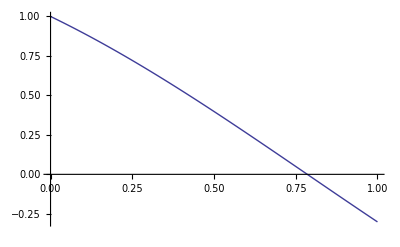

```mathematica
Plot[f[x],{x,0,1}]
```

## Fraction Generator (for limit practice)

```mathematica
a=RandomInteger[{-9,9}]/10
b=RandomInteger[{-9,9}]
c=RandomInteger[{-9,9}]
Expand[(x-a)(x-b)]/Expand[(x-a)(x-c)]
TeXForm[N[Expand[(x-a)(x-b)]/Expand[(x-a)(x-c)]]]
Simplify[(a-b)/(a-c)]
```

-4/5

9

-5

(-36/5-(41 x)/5+x^2)/(4+(29 x)/5+x^2)

-7/3

\frac{x^2-8.2 x-7.2}{x^2+5.8 x+4.}

```mathematica
f[x_]:=(-36/5-(41 x)/5+x^2)/(4+(29 x)/5+x^2)
```

```mathematica
TeXForm[TableForm[Table[{h,f[h]},{h,{-.81,-.801,-.79,-.799}}]]]
```

\begin{array}{cc}
 -0.81 & -2.34129 \\
 -0.801 & -2.33413 \\
 -0.79 & -2.32542 \\
 -0.799 & -2.33254
\end{array}

## Differentiation

#### Implicit Differentiation

```mathematica
Clear[x,y]
```

```mathematica
function[x_,y_]:=x^2 +y^2+ x y
sols=Simplify[Solve[Dt[function[x,y],x]==0,Dt[y,x]]]
Print[TeXForm[function[x,y]]]
Print[TeXForm[Dt[y,x]/.sols[[1]]]]
(Dt[y,x]/.sols[[1]])/.{x->(4+3Sqrt[3])/2,y->3/2}//Simplify
```

{{Dt[y,x]→-(2 x+y)/(x+2 y)}}

x^2+x y+y^2

-\frac{2 x+y}{x+2 y}

1/73 (-56-27 √3)

```mathematica
Dt[y,x]/.sols[[1]]
```

-y^(3/5)/x^(3/5)

```mathematica
Solve[(1/10.)^(2/5)+y^(2/5)==1,y]//Simplify
```

{{y→0.281059}}

```mathematica
(Dt[y,x]/.sols[[1]])/.{x->.1,y->.281}
```

-1.85876

#### Compute tangent lines

```mathematica
g[x_]:=(Cos[x]-8x)/(x+1)
point={0,2};
g'[point[[1]]]
```

-9

#### Extreme Values on Closed Interval

```mathematica
g[x]:=x
f[x_]:=x^2-3x+9
a=-2;
b=5;
sols=Solve[f'[x]==0,x];
special=Flatten[{a,b,x/.sols}]
values=f[special]
N[special]
N[values]
```

{-2,5,3/2}

{19,19,27/4}

{-2.,5.,1.5}

{19.,19.,6.75}

```mathematica
f[x_]:=Sin[x]
a=-Pi/2;
b=Pi/2;
Solve[f'[x]==(f[b]-f[a])/(b-a),x]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-ArcCos[2/π]},{x→ArcCos[2/π]}}

## Newtons’ Method

```mathematica
Expand[(x-1)(x-2)(x+1)(x+3)]
```

6-x-7 x^2+x^3+x^4

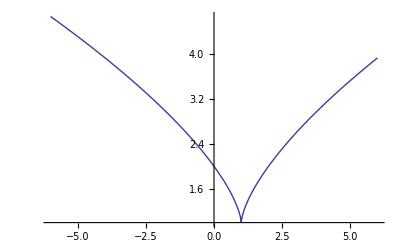

```mathematica
f[x_]:=((x-1)^2)^(1/3)+1
Plot[f[x],{x,-6,6}]
```

```mathematica
x0=2.;
iterations=10;
newtonslist={x0};
For[i=1,i≤iterations,i++,
xtemp=newtonslist[[i]]-f[newtonslist[[i]]]/f'[newtonslist[[i]]];
newtonslist=Append[newtonslist,xtemp];
];
newtonslist
```

{2.,3.,1.,2.,3.,1.,2.,3.,1.,2.,3.}

```mathematica
Clear[a,b,c,d]
```

```mathematica
f[x_]:=(x-1)(x-4)(x-3)+2
```

```mathematica
x2:=x1-f[x1]/f'[x1]
```

```mathematica
(*f[x_]:=(x-a)(x-b)(x-c)+d*)
f[x_]:=x^3-3x^2+x+3
Solve[x2-f[x2]/f'[x2]==x1,x1]
```

{{x1→1},{x1→2},{x1→1/4 (3+√11-2 √(-1/5+(3 √11)/10))},{x1→1/4 (3+√11+2 √(-1/5+(3 √11)/10))},{x1→1/4 (3-√11-ⅈ √(2/5 (2+3 √11)))},{x1→1/4 (3-√11+ⅈ √(2/5 (2+3 √11)))},{x1→1-(9-√57)^(1/3)/3^(2/3)-2/(3 (9-√57))^(1/3)},{x1→1+((1+ⅈ √3) (9-√57)^(1/3))/(2 3^(2/3))+(1-ⅈ √3)/(3 (9-√57))^(1/3)},{x1→1+((1-ⅈ √3) (9-√57)^(1/3))/(2 3^(2/3))+(1+ⅈ √3)/(3 (9-√57))^(1/3)}}

```mathematica
Clear[a,b,c,d,e]
```

```mathematica
f[x_]:=a x^4+b x^3+c x^2+d x+e
```

```mathematica
Solve[{f[1]/f'[1]==-1,f[2]/f'[2]==-1,f[3]/f'[3]==2},{a,b,c}]/.{d->1248/8,e->1248/8}
```

{{a→-17,b→130,c→-301}}

```mathematica
f[x_]:=-17x^4+130x^3-301x^2+156x+156
```

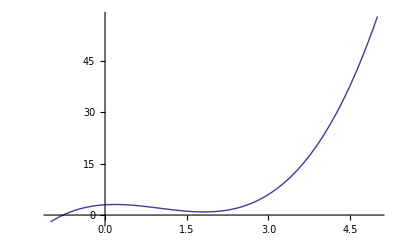

```mathematica
Plot[f[x],{x,-1,5}]
```

## Numerical Integration

```mathematica
Trap[f_,a_,b_,n_]:=((b-a)/n/2)*(f[a]+f[b]+2*Sum[f[a+i(b-a)/n],{i,1,n-1}])
Simp[f_,a_,b_,n_]:=((b-a)/n/3)*(f[a]+f[b]+2*Sum[f[a+i(b-a)/n],{i,2,n-2,2}]+4*Sum[f[a+i(b-a)/n],{i,1,n-1,2}])
```

```mathematica
Simp[1/(1+#^2)&,0,1,4]//N
```

0.785392

```mathematica
AverageValue[f_,a_,b_]:=Integrate[f[x],{x,a,b}]/(b-a)
```

```mathematica
MVT[f_,a_,b_]:=Solve[f[c]==Integrate[f[x],{x,a,b}]/(b-a),c]
```

```mathematica
LHR[f_,a_,b_,n_]:=(
dx=(b-a)/n;
Sum[f[a+(i-1)dx]*dx,{i,1,n}])
RHR[f_,a_,b_,n_]:=(
dx=(b-a)/n;
Sum[f[a+(i)dx]*dx,{i,1,n}])
MPR[f_,a_,b_,n_]:=(
dx=(b-a)/n;
Sum[f[((a+(i-1)dx)+(a+(i)dx))/2]*dx,{i,1,n}])
Simpsons[list_]:=(
sn=Length[list];
sa=list[[1,1]];
sb=list[[sn,1]];
sdx=(sb-sa)/(sn-1);
sdx/3*(list[[1,2]]+list[[sn,2]]+4Sum[list[[si,2]],{si,2,sn-1,2}]+2Sum[list[[si,2]],{si,3,sn-2,2}]))
```

```mathematica
(5^3*300)/(12*315^3)//N
```

0.0000999812

```mathematica
f[x_]:=x^4
a=0;
b=5;
Trap[f,a,b,3500]//Simplify
N[%,10]
Simp[f,a,b,46]//Simplify
N[%]
Integrate[f[x],{x,a,b}]
N[%]
```

300125040833333/480200000000

625.000085

4197615625/6716184

625.

625

625.

```mathematica
f[x_]:=Cos[x]
Simp[f,0,Pi/2,6]//N
```

1.00003

## Integration Creator/ TEX creator

```mathematica
f[x_]:=(x-2)/Sqrt[Expand[(x-3)^2-1]]
filename=StringJoin["06_01_ex_",ToString[i],".tex"]
(*str=OpenWrite["06_01_ex_09.tex"];*)
str=OpenWrite[filename]
i=i+1;
intstring1="{$\ds \int ";
intstring1=StringJoin[intstring1,ToString[TeXForm[f[x]]],"\ dx $}"]
intstring2=StringJoin["{$",ToString[TeXForm[Integrate[f[x],x]]],"$}"];
WriteString[str,intstring1];
Write[str];
WriteString[str,intstring2];
Close[str];
```

06_01_ex_73.tex

OutputStream[06_01_ex_73.tex,518]

{$\ds \int \frac{x-2}{\sqrt{x^2-6 x+8}} dx $}

```mathematica
i=10;
filename=StringJoin["06_01_ex_0",ToString[i],".tex"]
```

06_01_ex_010.tex

#### Writing Lists to a File

```mathematica
(*C:\\Users\\hartmangn\\Documents*)
```

```mathematica
SetDirectory["C:\\Documents and Settings\\hartmangn\\My Documents\\Text Projects\\Calculus\\exercises"]
```

C:\Documents and Settings\hartmangn\My Documents\Text Projects\Calculus\exercises

```mathematica
str=OpenWrite["06_01_ex_04.tex"]
WriteString[str,intstring1];
Write[str];
WriteString[str,intstring2];
Close[str];
```

OutputStream[06_01_ex_04.tex,447]

```mathematica
f[x_]:=Piecewise[{{x^2-2x+3,x≤1},{x,x>1}}]
```

```mathematica
intstring
```

{$\ds \int 3 x^2 \left(x^3-5\right)^7 dx $}{$3 \left(\frac{x^{24}}{24}-\frac{5 x^{21}}{3}+\frac{175 x^{18}}{6}-\frac{875 x^{15}}{3}+\frac{21875 x^{12}}{12}-\frac{21875 x^9}{3}+\frac{109375 x^6}{6}-\frac{78125 x^3}{3}\right)$}

```mathematica
g[x_]:=1/Expand[(x-1)^2+7]
```

```mathematica
g[x]
```

1/(8-2 x+x^2)

```mathematica
Show[ContourPlot3D[{x^2+y^2-z^2/4==0,z==-1/2x+4},{x,-4,4},{y,-4,4},{z,-7,8},ContourStyle->Opacity[.5],Mesh->None,Axes->False,Boxed->False,ViewPoint->{5,-10,2}],ParametricPlot3D[{32/15Cos[t]-8/15,8/Sqrt[15]Sin[t],-1/2(32/15Cos[t]-8/15)+4},{t,0,2Pi},PlotStyle->Thickness[.01]]]
```

## Conic Sections

```mathematica
Export["conic_ellipse.png",Show[ContourPlot3D[{x^2+y^2-z^2/4==0,z==-1/2x+4},{x,-5,5},{y,-5,5},{z,-8,8},ContourStyle->Opacity[.5],Mesh->None,Axes->False,Boxed->False,ViewPoint->{5,-10,2},ColorFunction->White],ParametricPlot3D[{32/15Cos[t]-8/15,8/Sqrt[15]Sin[t],-1/2(32/15Cos[t]-8/15)+4},{t,0,2Pi},PlotStyle->Thickness[.01]]]]
```

conic_ellipse.png

```mathematica
Export["conic_parabola.png",Show[ContourPlot3D[{x^2+y^2-z^2/4==0,z==-2x+2},{x,-5,5},{y,-5,5},{z,-8,8},Mesh->None,ContourStyle->Opacity[.5],Axes->False,Boxed->False,ViewPoint->{5,-10,2},ColorFunction->White],ParametricPlot3D[{.5(1-t^2),t,-2(.5(1-t^2))+2},{t,-2.65,2.65},PlotStyle->Thickness[.01]]]]
```

conic_parabola.png

```mathematica
Export["conic_hyperbola.png",Show[ContourPlot3D[{x^2+y^2-z^2/4==0,x==1},{x,-5,5},{y,-5,5},{z,-8,8},Mesh->None,ContourStyle->Opacity[.5],Axes->False,Boxed->False,ViewPoint->{5,-10,2},ColorFunction->White],ParametricPlot3D[{{1,Sqrt[t^2/4-1],t},{1,-Sqrt[t^2/4-1],t}},{t,-8,8},PlotStyle->Thickness[.01]]]]
```

conic_hyperbola.png

```mathematica
Export["conic_circle.png",Show[ContourPlot3D[{x^2+y^2-z^2/4==0,z==4},{x,-5,5},{y,-5,5},{z,-8,8},Mesh->None,ContourStyle->Opacity[.5],Axes->False,Boxed->False,ViewPoint->{5,-10,2},ColorFunction->White],ParametricPlot3D[{{2Cos[t],2Sin[t],4}},{t,0,2Pi},PlotStyle->Thickness[.01]]]]
```

conic_circle.png

```mathematica
Export["conic_oneline.png",Show[ContourPlot3D[{x^2+y^2-z^2/4==0,z==-2x},{x,-5,5},{y,-5,5},{z,-8,8},Mesh->None,ContourStyle->Opacity[.5],Axes->False,Boxed->False,ViewPoint->{5,-10,2},ColorFunction->White],ParametricPlot3D[{{t,0,-2t}},{t,-4,4},PlotStyle->Thickness[.01]]]]
```

conic_oneline.png

```mathematica
Export["conic_crossedlines.png",Show[ContourPlot3D[{x^2+y^2-z^2/4==0,x==0},{x,-5,5},{y,-5,5},{z,-8,8},Mesh->None,ContourStyle->Opacity[.5],Axes->False,Boxed->False,ViewPoint->{5,-10,2},ColorFunction->White],ParametricPlot3D[{{0,t,2t},{0,t,-2t}},{t,-4,4},PlotStyle->Thickness[.01]]]]
```

conic_crossedlines.png

```mathematica
Export["conic_singlept.png",Show[ContourPlot3D[{x^2+y^2-z^2/4==0,z==0},{x,-5,5},{y,-5,5},{z,-8,8},Mesh->None,ContourStyle->Opacity[.5],Axes->False,Boxed->False,ViewPoint->{5,-10,2},ColorFunction->White],ParametricPlot3D[{{.1Cos[t],.1Sin[t],0}},{t,0,2Pi},PlotStyle->Thickness[.01]]]]
```

conic_singlept.png

## Contour Plots

***  See also PointPlot Generator section ***

```mathematica
p1=Plot3D[(9x^2+4y^2)/Exp[x^2+y^2],{x,-2,2},{y,-2,2}];
```

```mathematica
cont=ContourPlot[(9x^2+4y^2)/Exp[x^2+y^2],{x,-2,2},{y,-2,2},Contours->15,Axes->False,PlotPoints->30,PlotRangePadding->0,Frame->False,ColorFunction->"DarkRainbow"]
```

```mathematica
level=-2;gr=Graphics3D[{Texture[cont],EdgeForm[],Polygon[{{-2,-2,level},{2,-2,level},{2,2,level},{-2,2,level}},VertexTextureCoordinates->{{0,0},{1,0},{1,1},{0,1}}]},Lighting->"Neutral"];
```

```mathematica
Show[p1,gr,PlotRange->All,BoxRatios->{1,1,.6},FaceGrids->{Back,Left}]
```

## Writing Parametric Graphs in TikZ

#### Writing plot to a File

```mathematica
SetDirectory["C:\\Documents and Settings\\hartmangn\\My Documents\\Text Projects\\Calculus\\figures"]
```

C:\Documents and Settings\hartmangn\My Documents\Text Projects\Calculus\figures

```mathematica
fstring="1/t";
gstring="sin(t)";
```

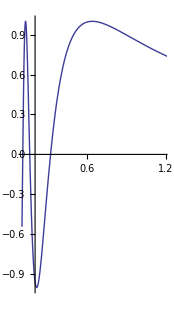

```mathematica
fstring="1/t";
gstring="sin(t)";
fstringz="1/x";
gstringz="sin(x)";
f[t_]:=Evaluate[ToExpression[fstring]]
g[t_]:=Evaluate[ToExpression[gstring]]
a=.1;
b=10;
c=5;
ParametricPlot[{f[x],Sin[x]},{x,a,b}]
```

```mathematica
{1/4,Sin[4]}//N
{1/(4.01),Sin[4.01]}//N
```

{0.25,-0.756802}

{0.249377,-0.763301}

```mathematica
xmin=-.5;
xmax=1.5;
ymin=-1.1;
ymax=1.1;
filename="09_02_ex_10";
SetDirectory["C:\\Documents and Settings\\hartmangn\\My Documents\\Text Projects\\Calculus\\figures"];
str=OpenWrite["fig_"<>filename<>".tex"];
WriteString[str,"\\begin{tikzpicture}"];
Write[str];
WriteString[str,"\\begin{axis}[width=\\marginparwidth+25pt,tick label style={font=\\scriptsize},axis y line=middle,axis x line=middle,name=myplot,
ymin="<>ToString[ymin]<>",ymax="<>ToString[ymax]<>",xmin="<>ToString[xmin]<>",xmax="<>ToString[xmax]<>"]"];
Write[str];
Write[str];
WriteString[str,"\\addplot [thick, smooth,domain="<>ToString[a]<>":"<>ToString[b]<>",samples=30] ({"<>fstringz<>"},{"<>gstringz<>"});"];
Write[str];
WriteString[str,"\\draw[>=latex,->,thick] (axis cs:"<>ToString[f[c]]<>","<>ToString[g[c]]<>")-- (axis cs:"<>ToString[f[c+.01]]<>","<>ToString[g[c+.01]]<>");"];
Write[str];
WriteString[str,"\\end{axis}"];
Write[str];
WriteString[str,"\\node [right] at (myplot.right of origin) {\\scriptsize $x$};"];
Write[str];
WriteString[str,"\\node [above] at (myplot.above origin) {\\scriptsize $y$};
"];
Write[str];
WriteString[str,"\\end{tikzpicture}"];
Close[str];
SetDirectory["C:\\Documents and Settings\\hartmangn\\My Documents\\Text Projects\\Calculus\\exercises"];
str=OpenWrite[filename<>".tex"];
WriteString[str,"{$x="<>fstring<>"$,\\quad $y="<>gstring<>"$,\\quad $"<>ToString[a]<>"\\leq t \\leq "<>ToString[b]<>"$}"];
Write[str];
WriteString[str,"{\\begin{minipage}{\\linewidth}
\\includegraphics{figures/fig"<>filename<>"}\\end{minipage}
}"];
Close[str];
```

```mathematica
Close["fig_09_02_ex_09.tex"]
```

fig_09_02_ex_09.tex

```mathematica
f[x_]:=Piecewise[{{x^2-2x+3,x≤1},{x,x>1}}]
```

```mathematica
intstring
```

{$\ds \int 3 x^2 \left(x^3-5\right)^7 dx $}{$3 \left(\frac{x^{24}}{24}-\frac{5 x^{21}}{3}+\frac{175 x^{18}}{6}-\frac{875 x^{15}}{3}+\frac{21875 x^{12}}{12}-\frac{21875 x^9}{3}+\frac{109375 x^6}{6}-\frac{78125 x^3}{3}\right)$}

```mathematica
g[x_]:=1/Expand[(x-1)^2+7]
```

```mathematica
g[x]
```

1/(8-2 x+x^2)

```mathematica
Show[ContourPlot3D[{x^2+y^2-z^2/4==0,z==-1/2x+4},{x,-4,4},{y,-4,4},{z,-7,8},ContourStyle->Opacity[.5],Mesh->None,Axes->False,Boxed->False,ViewPoint->{5,-10,2}],ParametricPlot3D[{32/15Cos[t]-8/15,8/Sqrt[15]Sin[t],-1/2(32/15Cos[t]-8/15)+4},{t,0,2Pi},PlotStyle->Thickness[.01]]]
```

#### Writing 3D Surface to File for PGFPlots

```mathematica
xmin=-1.5;
xmax=1.5;
xstep=(xmax-xmin)/20;
ymin=-1.5;
ymax=1.5;
zmin=-2;
ystep=(ymax-ymin)/20;
f[x_,y_]:=-x^4-y^4+4x y
filename="surface_test";
SetDirectory["C:\\Documents and Settings\\hartmangn\\My Documents\\Text Projects\\Calculus\\figures"];
str=OpenWrite["fig_"<>filename<>"_data"<>".tex"];
Do[Do[WriteString[str,ToString[mynumstyle[i]]<>" "<>ToString[mynumstyle[j]]<>" "<>ToString[mynumstyle[f[i,j]]]];Write[str];,{j,ymin,ymax,ystep}];Write[str];,{i,xmin,xmax,xstep}];
Close[str];
(*SetDirectory["C:\\Documents and Settings\\hartmangn\\My Documents\\Text Projects\\Calculus\\exercises"];
str=OpenWrite[filename<>".tex"];
WriteString[str,"{$x="<>fstring<>"$,\\quad $y="<>gstring<>"$,\\quad $"<>ToString[a]<>"\\leq t \\leq "<>ToString[b]<>"$}"];
Write[str];
WriteString[str,"{\\begin{minipage}{\\linewidth}
\\includegraphics{figures/fig"<>filename<>"}\\end{minipage}
}"];
Close[str];
*)
```

## Drawing Graphs with Velocity, Acc Vectors w/ TikZ

```mathematica
SetOptions[$FrontEndSession,"ExportTypesetOptions"->{"PageWidth"->500}]
```

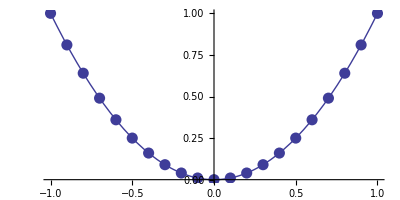

```mathematica
s[t_]:={t,t^2}
v[t_]:=s'[t]
a[t_]:=v'[t]
Show[ParametricPlot[s[t],{t,-1,1}],ListPlot[Table[s[i],{i,-1,1,.1}],PlotStyle->PointSize[.02]]]
```

```mathematica
s[-.9]
s[-.89]
```

{-0.9,0.81}

{-0.89,0.7921}

```mathematica
string={};
Do[string=StringJoin[string,"\\draw [thick,->,{\\colortwo}] (axis cs:",ToString[s[i][[1]]],",",ToString[s[i][[2]]],")--(axis cs:",ToString[s[i][[1]]+v[i][[1]]],",",ToString[s[i][[2]]+v[i][[2]]],");"];,{i,-1,1,.5}]
string
```

\draw [thick,->,{\colortwo}] (axis cs:-1.,1.)--(axis cs:2.,-5.);\draw [thick,->,{\colortwo}] (axis cs:-0.125,0.015625)--(axis cs:0.625,-0.171875);\draw [thick,->,{\colortwo}] (axis cs:0.,0.)--(axis cs:0.,0.);\draw [thick,->,{\colortwo}] (axis cs:0.125,0.015625)--(axis cs:0.875,0.203125);\draw [thick,->,{\colortwo}] (axis cs:1.,1.)--(axis cs:4.,7.);

```mathematica
string={};
Do[string=StringJoin[string,"\\draw [thick,->] (axis cs:",ToString[s[i][[1]]],",",ToString[s[i][[2]]],")--(axis cs:",ToString[s[i][[1]]+a[i][[1]]],",",ToString[s[i][[2]]+a[i][[2]]],");"];,{i,-1,1,.5}]
string
```

\draw [thick,->] (axis cs:-1.,1.)--(axis cs:-7.,31.);\draw [thick,->] (axis cs:-0.125,0.015625)--(axis cs:-3.125,1.89063);\draw [thick,->] (axis cs:0.,0.)--(axis cs:0.,0.);\draw [thick,->] (axis cs:0.125,0.015625)--(axis cs:3.125,1.89063);\draw [thick,->] (axis cs:1.,1.)--(axis cs:7.,31.);

```mathematica
string={};
Do[string=StringJoin[string,"\\filldraw (axis cs:",ToString[s[i][[1]]],",",ToString[s[i][[2]]],") circle (1.5pt);"];,{i,-1,1,.5}];
string
```

\filldraw (axis cs:-1.,1.) circle (1.5pt);\filldraw (axis cs:-0.5,0.25) circle (1.5pt);\filldraw (axis cs:0.,0.) circle (1.5pt);\filldraw (axis cs:0.5,0.25) circle (1.5pt);\filldraw (axis cs:1.,1.) circle (1.5pt);

## 3D Graphics & Asymptote

Enter the data from the “Get Current View” of Adobe Reader/Acrobat when viewing a 3D graphic. Copy the output between “VIEW” and “END” as the string argument. Copy/Paste the output of the function into the \includemedia command, or the mfigurethree graphics, etc.

```mathematica
mfigureoutput[s_]:=(
coo=StringCases[s,RegularExpression["COO.+\n"]];
c2c=StringCases[s,RegularExpression["C2C.+\n"]];
roo=StringCases[s,RegularExpression["ROO.+\n"]];
ortho=StringCases[s,RegularExpression["ORTHO.+\n"]];
roll=StringCases[s,RegularExpression["ROLL.+\n"]];
If[coo≠{},coo=StringTake[coo[[1]],{5,StringLength[coo[[1]]]-1}],coo=" "];
If[c2c≠{},c2c=StringTake[c2c[[1]],{5,StringLength[c2c[[1]]]-1}],c2c=" "];
If[roo≠{},roo=StringTake[roo[[1]],{5,StringLength[roo[[1]]]-1}],roo=" "];
If[ortho≠{},ortho=StringTake[ortho[[1]],{7,StringLength[ortho[[1]]]-1}],ortho=" "];
If[roll≠{},roll=StringTake[roll[[1]],{6,StringLength[roll[[1]]]-1}],roll="0"];
"3Droll="<>roll<>",\n"<>"3Dortho="<>ortho<>",\n"<>"3Dc2c="<>c2c<>",\n"<>"3Dcoo="<>coo<>",\n"<>"3Droo="<>roo<>",\n")
```

```mathematica
mfigureoutputZeroroll[s_]:=(
coo=StringCases[s,RegularExpression["COO.+\n"]];
c2c=StringCases[s,RegularExpression["C2C.+\n"]];
roo=StringCases[s,RegularExpression["ROO.+\n"]];
ortho=StringCases[s,RegularExpression["ORTHO.+\n"]];
roll=StringCases[s,RegularExpression["ROLL.+\n"]];
If[coo≠{},coo=StringTake[coo[[1]],{5,StringLength[coo[[1]]]-1}],coo=" "];
If[c2c≠{},c2c=StringTake[c2c[[1]],{5,StringLength[c2c[[1]]]-1}],c2c=" "];
If[roo≠{},roo=StringTake[roo[[1]],{5,StringLength[roo[[1]]]-1}],roo=" "];
If[ortho≠{},ortho=StringTake[ortho[[1]],{7,StringLength[ortho[[1]]]-1}],ortho=" "];
If[roll≠{},roll="0",roll="0"];
"3Droll="<>roll<>",\n"<>"3Dortho="<>ortho<>",\n"<>"3Dc2c="<>c2c<>",\n"<>"3Dcoo="<>coo<>",\n"<>"3Droo="<>roo<>",\n")
```

```mathematica
mfigureoutput["VIEW%=insert optional name here
  COO=21.82058334350586 66.31769561767578 47.81545639038086
  C2C=0.9118747115135193 -0.1974218785762787 0.35987377166748047
  ROO=149.99999973566392
  ROLL=0.12234160136132792
  ORTHO=0.004824123345315456
  LIGHTS=Headlamp
END"]
```

3Droll=0.12234160136132792,
3Dortho=0.004824123345315456,
3Dc2c=0.9118747115135193 -0.1974218785762787 0.35987377166748047,
3Dcoo=21.82058334350586 66.31769561767578 47.81545639038086,
3Droo=149.99999973566392,

```mathematica
CopyToClipboard[mfigureoutput[NotebookGet[ClipboardNotebook[]][[1,1,1]]]]
```

```mathematica
CopyToClipboard[mfigureoutputZeroroll[NotebookGet[ClipboardNotebook[]][[1,1,1]]]]
```

3Droll=0,
3Dortho=0.004519372712820768,
3Dc2c=0.5538474321365356 0.6883921027183533 0.46836861968040466,
3Dcoo=36.11201095581055 39.69871139526367 85.62228393554688,
3Droo=149.99999263453046,

## Compressing Final Output

```mathematica
(* from StackExchange   "gs -sDEVICE=pdfwrite -dCompatibilityLevel=1.4 -dNOPAUSE -dQUIET -dBATCH -sOutputFile=foo-compressed.pdf foo.pdf"
*)
```

```mathematica
SetDirectory["C:\\Users\\hartmangn\\Documents\\Text Projects\\Calculus"]
```

C:\Users\hartmangn\Documents\Text Projects\Calculus

```mathematica
filename="Calculus_Question_File.pdf";
newFilename="Calculus_Question_File_compressed.pdf";
```

```mathematica
compressCommand="gswin64 -sDEVICE=pdfwrite -dCompatibilityLevel=1.7 -dNOPAUSE -dQUIET -dBATCH -sOutputFile="<>newFilename<>" "<>filename;
```

```mathematica
program="C:\\Program Files\\gs\\gs9.15\\bin\\gswin64";
```

```mathematica
compressCommand="\"C:\\Program Files\\gs\\gs9.15\\bin\\gswin64\" -sDEVICE=pdfwrite -dCompatibilityLevel=1.4 -dNOPAUSE -dQUIET -dBATCH -sOutputFile="<>newFilename<>" "<>filename
```

"C:\Program Files\gs\gs9.15\bin\gswin64" -sDEVICE=pdfwrite -dCompatibilityLevel=1.4 -dNOPAUSE -dQUIET -dBATCH -sOutputFile=Calculus_Question_File_compressed.pdf Calculus_Question_File.pdf

```mathematica
Run[compressCommand]
```

0

## Printing All Questions in Text

```mathematica
SetDirectory["C:\\Users\\hartmangn\\Documents\\Text Projects\\Calculus\\exercises"]
```

C:\Users\hartmangn\Documents\Text Projects\Calculus\exercises

```mathematica
outputName="All_Questions.tex";
```

```mathematica
str=OpenWrite[outputName];
```

```mathematica
chapterCounter=0;
sectionCounter=0;
WriteString[str,"\\setcounter{chapter}{0}\n\\setcounter{section}{0}"];
Write[str];
Do[
If[ToExpression[StringTake[files[[i]],{1,2}]]>chapterCounter,chapterCounter++;WriteString[str,"\\addtocounter{chapter}{1}"];WriteString[str,"\\setcounter{section}{0}"];];
(*If[ToExpression[StringTake[files[[1]],{4,5}]]>sectionCounter,sectionCounter++];*)
WriteString[str,"\\addtocounter{section}{1}"];
Write[str];
WriteString[str,"\\printexercises{exercises/"<>files[[i]]<>"}"];
Write[str];,
{i,1,Length[files]}]
```

```mathematica
Close[str]
```

All_Questions.tex

## Closed Curve Generator

#### Option 1:

```mathematica
x[t_]:=.5Sin[10t]+1
y[t_]:=x[t]
ParametricPlot[{x[t]Cos[t],y[t]Sin[t]},{t,0,2Pi}];
xvals=Sort[RandomReal[{0,2Pi},5]];
pts=Table[{x[t]Cos[t],y[t]Sin[t]},{t,xvals}];
f=BSplineFunction[pts,SplineClosed->True];
f3[t_]:=Flatten[{f[t],0}]
ParametricPlot3D[f3[t],{t,0,1}]
```

#### Option 2:

```mathematica
f[x_]:=Piecewise[{{Sin[x],Mod[x,4 Pi]<Pi},{-1/2 Sin[2 x],Mod[x,4 Pi]≥Pi&&Mod[x,4 Pi]<2 Pi},{-Sin[x],Mod[x,4 Pi]≥2 Pi&&Mod[x,4 Pi]<3 Pi},{1/2 Sin[2 x],Mod[x,4 Pi]≥3 Pi}}]
blurb[x_,a_,b_]:=Flatten[{(1+a f[b x]) {Cos[x],Sin[x]},0}]
```

```mathematica
Manipulate[ParametricPlot3D[blurb[x,a,b],{x,0,2 Pi}],{{a,.5},-1,1},{{b,2},1,10,1}]
```

## Rectangular To Spherical To Cylindrical Conversions

```mathematica
r2c[{x_,y_,z_}]:={Sqrt[x^2+y^2],Mod[ArcTan[x,y],2Pi],z}
c2r[{r_,t_,z_}]:={r Cos[t],r Sin[t],z}
r2s[{x_,y_,z_}]:={Sqrt[x^2+y^2+z^2],Mod[ArcTan[x,y],2Pi],ArcCos[z/Sqrt[x^2+y^2+z^2]]}
s2r[{r_,t_,p_}]:={r Sin[p]Cos[t],r Sin[p]Sin[t],r Cos[p]}
s2c[{r_,t_,p_}]:={r Sin[p],t,r Cos[p]}
c2s[{r_,t_,z_}]:={Sqrt[r^2+z^2],t,ArcTan[z,r]}
```

```mathematica
r2c[{2,2,1}]
r2s[{2,2,1}]
```

{2 √2,π/4,1}

{3,π/4,ArcCos[1/3]}

```mathematica
r2c[{1,Sqrt[3],0}]
r2s[{1,Sqrt[3],0}]
```

{2,π/3,0}

{2,π/3,π/2}

```mathematica
r2c[{-Sqrt[3],1,0}]
r2s[{-Sqrt[3],1,0}]
```

{2,(5 π)/6,0}

{2,(5 π)/6,π/2}

```mathematica
r2c[{0,1,1}]
r2s[{0,1,1}]
```

{1,π/2,1}

{√2,π/2,π/4}

```mathematica
r2c[{-1,0,1}]
r2s[{-1,0,1}]
```

{1,π,1}

{√2,π,π/4}

```mathematica
r2c[{-1,0,-1}]
r2s[{-1,0,-1}]
```

{1,π,-1}

{√2,π,(3 π)/4}

```mathematica
c2r[{2,Pi/4,2}]
c2s[{2,Pi/4,2}]
```

{√2,√2,2}

{2 √2,π/4,π/4}

```mathematica
c2r[{3,3Pi/2,-4}]
c2s[{3,3Pi/2,-4}]
```

{0,-3,-4}

{5,(3 π)/2,π-ArcTan[3/4]}

```mathematica
c2r[{0,Pi,1}]
c2s[{0,Pi,1}]
```

{0,0,1}

{1,π,0}

```mathematica
c2r[{2,4Pi/3,0}]
c2s[{2,4Pi/3,0}]
```

{-1,-√3,0}

{2,(4 π)/3,π/2}

```mathematica
c2r[{5,Pi/2,-5}]
c2s[{5,Pi/2,-5}]
```

{0,5,-5}

{5 √2,π/2,(3 π)/4}

```mathematica
c2r[{0,0,-4}]
c2s[{0,0,-4}]
```

{0,0,-4}

{4,0,π}

```mathematica
s2r[{2,Pi/4,Pi/4}]
s2c[{2,Pi/4,Pi/4}]
```

{1,1,√2}

{√2,π/4,√2}

```mathematica
s2r[{1,0,0}]
s2c[{1,0,0}]
```

{0,0,1}

{0,0,1}

```mathematica
s2r[{5,3Pi/2,Pi/3}]
s2c[{5,3Pi/2,Pi/3}]
```

{0,-(5 √3)/2,5/2}

{(5 √3)/2,(3 π)/2,5/2}

```mathematica
s2r[{2,Pi/6,Pi/2}]
s2c[{2,Pi/6,Pi/2}]
```

{√3,1,0}

{2,π/6,0}

```mathematica
s2r[{3,Pi,Pi}]
s2c[{3,Pi,Pi}]
```

{0,0,-3}

{0,π,-3}

```mathematica
s2r[{0,Pi,0}]
s2c[{0,Pi,0}]
```

{0,0,0}

{0,π,0}